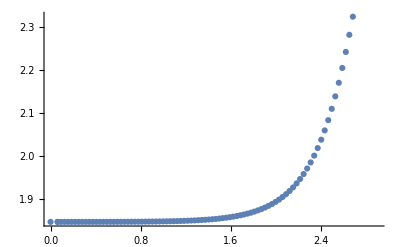

```mathematica
f4={{0,17.610224},{0.062500,17.603234},{0.062500,17.603234},{0.093750,17.653723},{0.125000,17.696613},{0.156250,17.742578},{0.187500,17.792407},{0.218750,17.845635},{0.250000,17.901589},{0.281250,17.959607},{0.312500,18.019085},{0.343750,18.079483},{0.375000,18.140325},{0.406250,18.201186},{0.437500,18.261691},{0.468750,18.321502},{0.500000,18.380316},{0.531250,18.437862},{0.562500,18.493895},{0.593750,18.548192},{0.625000,18.600551},{0.656250,18.650790},{0.687500,18.698742},{0.718750,18.744257},{0.750000,18.787197},{0.781250,18.827440},{0.812500,18.864874},{0.843750,18.899399},{0.875000,18.930925},{0.906250,18.959374},{0.937500,18.984677},{0.968750,19.006776},{1.000000,19.025621},{1.031250,19.041173},{1.062500,19.053404},{1.093750,19.062293},{1.125000,19.067832},{1.156250,19.070021},{1.187500,19.068872},{1.218750,19.064411},{1.250000,19.056672},{1.281250,19.045705},{1.312500,19.031572},{1.343750,19.014351},{1.375000,18.994136},{1.406250,18.971035},{1.437500,18.945180},{1.468750,18.916719},{1.500000,18.885823},{1.531250,18.852687},{1.562500,18.817532},{1.593750,18.780605},{1.625000,18.742187},{1.656250,18.702590},{1.687500,18.662162},{1.718750,18.621292},{1.750000,18.580410},{1.781250,18.539992},{1.812500,18.500566},{1.843750,18.462713},{1.875000,18.427072},{1.906250,18.394347},{1.937500,18.365306},{1.968750,18.340794},{2.000000,18.321731},{2.031250,18.309121},{2.062500,18.304055},{2.093750,18.307717},{2.125000,18.321390},{2.156250,18.346461},{2.187500,18.384423},{2.218750,18.436880},{2.250000,18.505556},{2.281250,18.592288},{2.312500,18.699038},{2.343750,18.827888},{2.375000,18.981045},{2.406250,19.160836},{2.437500,19.369710},{2.468750,19.610236},{2.500000,19.885100},{2.531250,20.197102},{2.562500,20.549163},{2.593750,20.944325},{2.625000,21.385763},{2.656250,21.876810},{2.687500,22.420996},{2.718750,23.022106},{2.750000,23.684273},{2.781250,24.412117},{2.812500,25.210930},{2.843750,26.086947},{2.875000,27.047693},{2.906250,28.102424}};
ff4={{0,15.762610},{0.062500,15.755620},{0.062500,15.755620},{0.093750,15.806107},{0.125000,15.848996},{0.156250,15.894959},{0.187500,15.944784},{0.218750,15.998008},{0.250000,16.053957},{0.281250,16.111969},{0.312500,16.171439},{0.343750,16.231828},{0.375000,16.292659},{0.406250,16.353508},{0.437500,16.413997},{0.468750,16.473791},{0.500000,16.532586},{0.531250,16.590111},{0.562500,16.646118},{0.593750,16.700386},{0.625000,16.752713},{0.656250,16.802914},{0.687500,16.850824},{0.718750,16.896292},{0.750000,16.939179},{0.781250,16.979362},{0.812500,17.016728},{0.843750,17.051175},{0.875000,17.082615},{0.906250,17.110967},{0.937500,17.136161},{0.968750,17.158137},{1.000000,17.176845},{1.031250,17.192243},{1.062500,17.204301},{1.093750,17.212995},{1.125000,17.218316},{1.156250,17.220261},{1.187500,17.218839},{1.218750,17.214071},{1.250000,17.205990},{1.281250,17.194639},{1.312500,17.180076},{1.343750,17.162375},{1.375000,17.141622},{1.406250,17.117921},{1.437500,17.091394},{1.468750,17.062183},{1.500000,17.030448},{1.531250,16.996375},{1.562500,16.960174},{1.593750,16.922080},{1.625000,16.882358},{1.656250,16.841306},{1.687500,16.799255},{1.718750,16.756574},{1.750000,16.713672},{1.781250,16.671001},{1.812500,16.629063},{1.843750,16.588408},{1.875000,16.549644},{1.906250,16.513437},{1.937500,16.480515},{1.968750,16.451678},{2.000000,16.427794},{2.031250,16.409810},{2.062500,16.398755},{2.093750,16.395745},{2.125000,16.401982},{2.156250,16.418768},{2.187500,16.447500},{2.218750,16.489676},{2.250000,16.546903},{2.281250,16.620890},{2.312500,16.713458},{2.343750,16.826540},{2.375000,16.962177},{2.406250,17.122527},{2.437500,17.309861},{2.468750,17.526568},{2.500000,17.775162},{2.531250,18.058292},{2.562500,18.378757},{2.593750,18.739540},{2.625000,19.143847},{2.656250,19.595167},{2.687500,20.097355},{2.718750,20.654713},{2.750000,21.272025},{2.781250,21.954365},{2.812500,22.706084},{2.843750,23.526892},{2.875000,24.397009},{2.906250,25.228805}};
F4=f4-ff4*Table[{0,1},{i,0,93}];
ListPlot[{F4}]
```

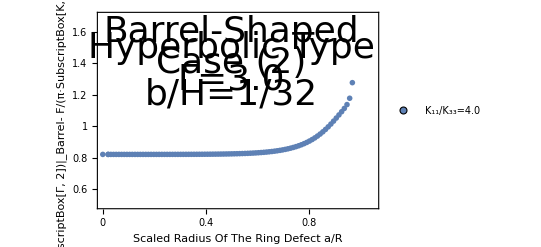

```mathematica
FF4=F4*Table[{1/3,4/9},{i,0,93}];
ListPlot[{FF4},PlotStyle->PointSize[0.01], Frame->{True, True, True, True}, FrameTicks->{{{0.6,0.8,1,1.2,1.4,1.6},None},{{0,0.2, 0.4, 0.6, 0.8,1.0},None}}, PlotRange->{{0,1.05},{0.5,1.7}},FrameLabel->{{"F/(π·SubscriptBox[K, 33] H SuperscriptBox[Γ, 2])|_Barrel- F/(π·SubscriptBox[K, 33] H SuperscriptBox[Γ, 2])|_Cylinder", None},{"Scaled Radius Of The Ring Defect a/R", None}},FrameTicksStyle->Directive[Black,36],FrameStyle->Thickness[0.005],LabelStyle->Directive[Black,36],PlotLegends->Placed[PointLegend[{"K_11/K_33=4.0"},LegendMarkers->{{Graphics[Disk[]],12}}],{Right,Bottom}],Epilog->{Text[Style["Barrel-Shaped",Directive[Black,36]],{0.5,1.6}],Text[Style["Hyperbolic Type",Directive[Black,36]],{0.5,1.5}],Text[Style["Case (2)",Directive[Black,36]],{0.5,1.4}],Text[Style["Γ=3.0",Directive[Black,36]],{0.5,1.3}],Text[Style["b/H=1/32",Directive[Black,36]],{0.5,1.2}]}]
```